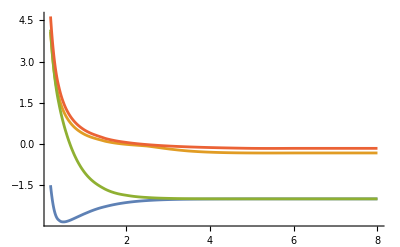

```mathematica
(* Radiative Quenching *)

(* All values in atomic units *)

(*electron mass *)
Subscript[m, e]=1;
(* Proton Mass *)
Subscript[m, p]=1836;
(* Reduced Mass *)
Subscript[m, μ]=Subscript[m, p]/2;
ℏ= 1;  
(*SpeedOfLight *)
c=137 ;
(* Boltzman constant *)
Subscript[k, B] = 3.167*^-6 ;
(* Atomic unit of temperature *)
atUofT = 3.1577464*^5;
 
(* Compute the eigenvalues A, p from the system of equations *)
(* RawData format R, p, A, E, E + 1/R *)
SetDirectory[NotebookDirectory[]];
vS1RawData = Import["./s1_state.mat"][[1]];
vS2RawData = Import["./s2_state.mat"][[1]];
vP2PlusRawData = Import["./p2uPlus_state.mat"][[1]];
vP2MinusRawData = Import["./p2uMinus_state.mat"][[1]];

(* Get values of R, E + 1/R *)
vS1Data=Table[{vS1RawData[[i]][[1]],vS1RawData[[i]][[5]]},{i,1,Length[vS1RawData]}];
vS2Data=Table[{vS2RawData[[i]][[1]],vS2RawData[[i]][[5]]},{i,1,Length[vS2RawData]}];
vP2PlusData=Table[{vP2PlusRawData[[i]][[1]],vP2PlusRawData[[i]][[5]]},{i,1,Length[vP2PlusRawData]}];
vP2MinusData=Table[{vP2MinusRawData[[i]][[1]],vP2MinusRawData[[i]][[5]]},{i,1,Length[vP2MinusRawData]}];

(* Last value of R in the computed data *)
lastR = vS1Data[[Length[vS1Data]]][[1]] + 1;

(* max distance between the nuclei *)
maxR=8;
(* what we consider as 'Large' r, i.e electron being far away from the nuclei *)
rMax = 15;

(* Extrapolate to maxR *)
vS1Data=Join[vS1Data,Table[{i,vS1Data[[Length[vS1Data]]][[2]]},{i,lastR,maxR,1}]];
vS2Data=Join[vS2Data,Table[{i,vS2Data[[Length[vS2Data]]][[2]]},{i,lastR,maxR,1}]];
vP2PlusData=Join[vP2PlusData,Table[{i,vP2PlusData[[Length[vP2PlusData]]][[2]]},{i,lastR,maxR,1}]];
vP2MinusData=Join[vP2MinusData,Table[{i,vP2MinusData[[Length[vP2MinusData]]][[2]]},{i,lastR,maxR,1}]];


(* 1sg state, potential curve *)
Subscript[v, s1]=Interpolation[Transpose[{vS1Data[[All,1]],vS1Data[[All,2]]}], InterpolationOrder->3];
(* 2sg state, potential curve *)
Subscript[v, s2]=Interpolation[Transpose[{vS2Data[[All,1]],vS2Data[[All,2]]}], InterpolationOrder->3];
(* 2P+ state *)
Subscript[v, p2p]=Interpolation[Transpose[{vP2PlusData[[All,1]],vP2PlusData[[All,2]]}], InterpolationOrder->3];
(* 2P- state *)
Subscript[v, p2m]=Interpolation[Transpose[{vP2MinusData[[All,1]],vP2MinusData[[All,2]]}], InterpolationOrder->3];


Plot[{Subscript[v, s1][r],Subscript[v, s2][r], Subscript[v, p2p][r], Subscript[v, p2m][r]},{r,0.2,maxR}, PlotLabels->Automatic, PlotRange->{5,-4}]


(* Compute the Dipole momement D(r) for the single value of R *)
singleDR[R_,p1_,a1_,p2_,a2_]:=Module[{lSol1,mSol1, lSol2,mSol2,norm1, norm2,dInt, ll1, ll2, mm1, mm2, L, M},
(* 1st wavefunction *)
(* x = λ, y = μ **)
lSol1=NDSolve[{(λ^2-1)L''[λ]+λ * L'[λ]+ (a1 +2 R λ -p1^2 λ^2)L[λ]==0 ,L[1.0001]==0,L'[1.0001]==1 },L[λ],{λ,1.0001,rMax}][[1]];mSol1=NDSolve[{(1-μ^2)M''[μ]-μ *M'[μ] - (a1 + p1^2 μ^2)M[μ]==0, M[0]==1,M'[0]==0}, M[μ],{μ,-.9999,.9999}][[1]];
(* 2nd wavefunction *) 
lSol2=NDSolve[{(λ^2-1)L''[λ]+λ * L'[λ]+ (a2+2 R λ -p2^2 λ^2)L[λ]==0 ,L[1.0001]==0,L'[1.0001]==1},L[λ],{λ,1.0001, rMax}][[1]];
mSol2=NDSolve[{(1-μ^2)M''[μ]-μ *M'[μ] - (a2 + p2^2 μ^2)M[μ]==0, M[0]==0,M'[0]==1}, M[μ],{μ,-.9999,.9999}][[1]];

(* To evaluate NDSolve output at a single point *)

(*
ll1[x_]:= L[λ]/. lSol1 /. λ-> x;
ll2[x_]:= L[λ]/. lSol2/. λ-> x;
mm1[y_]:= M[μ]/. mSol1 /. μ-> y;
mm2[y_]:= M[μ]/. mSol2 /. μ-> y;
*)

Print[Plot[L[λ]/. lSol1 ,{λ,1.0001,rMax}]];

(* σ = λ, θ = μ *)

(* Compute <ψ|ψ> = <Subscript[ψ, 1]|Subscript[ψ, 1]> + <Subscript[ψ, 2]|Subscript[ψ, 2]> *)
(* <Subscript[ψ, 1]|Subscript[ψ, 1]> *)
norm1=NIntegrate[Conjugate[(L[λ]/. lSol1)(M[μ]/. mSol1)](L[λ]/. lSol1)(M[μ]/. mSol1),{μ,-.9999,.9999},{λ,1.00001,rMax}];
(* <Subscript[ψ, 2]|Subscript[ψ, 2]> *)
norm2=NIntegrate[Conjugate[(L[λ]/. lSol2)(M[μ]/. mSol2)](L[λ]/. lSol2)(M[μ]/. mSol2),{μ,-.9999,.9999},{λ,1.00001,rMax}];

dInt=(R/2)1/Sqrt[norm1 norm2](
  NIntegrate[Conjugate[(L[λ]/. lSol1)(M[μ]/. mSol1)] (Sqrt[λ^2 μ^2+(λ^2-1)(1-μ^2) ])(L[λ]/. lSol2)(M[μ]/. mSol2),{λ,1.00001,rMax},{μ,-.9999,.9999}] 
);
Print[R, ":", dInt];
{R,dInt }
]


GetInputData[state1_, state2_]:=Module[{inputData, deltaV},
Switch[state1,
(* From State *)
"s1",
	(* To State *)
	Switch [state2,
	"s2",
		deltaV[r_]:=Abs[vs1[r]-vs2[r]];
		inputData = Transpose[
		{vS1RawData[[All,1]],vS1RawData[[All,2]],vS1RawData[[All,3]],vS1RawData[[All,2]],vS1RawData[[All,3]]}],
	"p+",
		deltaV[r_]:=Abs[Subscript[v, s1][r]-Subscript[v, p2p][r]];
		inputData = Transpose[
		{vS1RawData[[All,1]],vS1RawData[[All,2]],vS1RawData[[All,3]],vP2PlusRawData[[All,2]],vP2PlusRawData[[All,3]]}],
	"p-",
		deltaV=Abs[Subscript[v, s1][r]-Subscript[v, p2m][r]];
		inputData = Transpose[
		{vS1RawData[[All,1]],vS1RawData[[All,2]],vS1RawData[[All,3]],vP2MinusRawData[[All,2]],vP2MinusRawData[[All,3]]}],
	_,Throw["Invalid State"]],
"s2", 
	Switch [state2,
	"p+",
		deltaV[r_]:=Abs[Subscript[v, s2][r]-Subscript[v, p2p][r]];
		inputData = Transpose[
		{vS2RawData[[All,1]],vS2RawData[[All,2]],vS2RawData[[All,3]],vP2PlusRawData[[All,2]],vP2PlusRawData[[All,3]]}],
	"p-",
		deltaV=Abs[Subscript[v, s2][r]-Subscript[v, p2m][r]];
		inputData = Transpose[
		{vS2RawData[[All,1]],vS2RawData[[All,2]],vS2RawData[[All,3]],vP2MinusRawData[[All,2]],vP2MinusRawData[[All,3]]}],
	_,Throw["Invalid State"]],
_,Throw["Invalid State"]];
{inputData,deltaV}
];

{inputDataPlus,deltaV}=GetInputData["s1","p+"];
{inputDataMinus,deltaV}=GetInputData["s1","p-"];
```

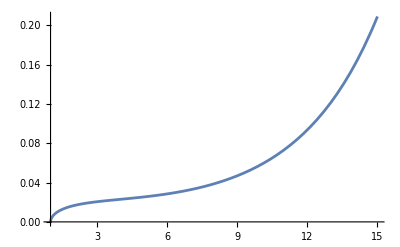

0.2:0.032289

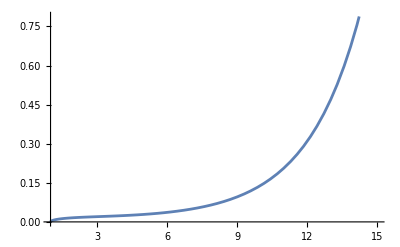

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.3:-2511.6

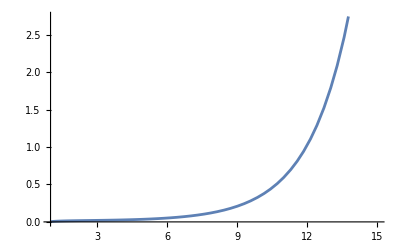

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

0.4:256.578

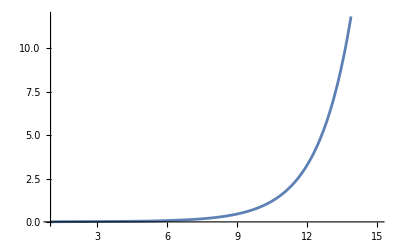

0.5:75.6485

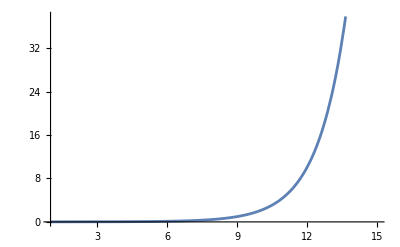

0.6:14.9705

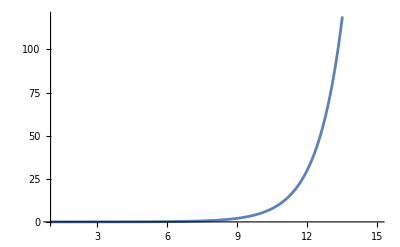

0.7:21610.4

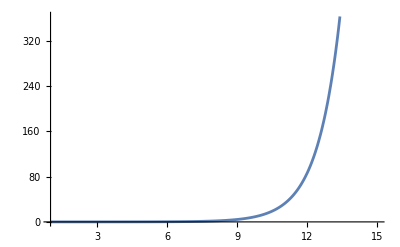

0.8:-1322.02

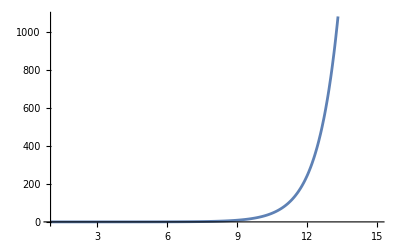

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.18632×10^-10 and 0.0000612342 for the integral and error estimates.

0.9:1.84775×10^-16

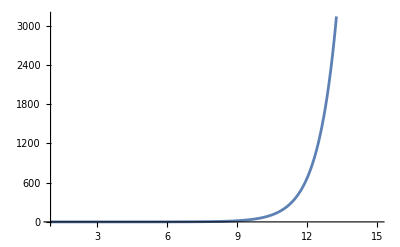

```mathematica
CalcDR[inputData_, maxRvalue_]:=Module[{allDR,dR},
allDR =Map[singleDR[#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]] &, inputData];
Print[ListPlot[allDR]];
dR =Interpolation[Transpose[{allDR[[All,1]],allDR[[All,2]]}], InterpolationOrder->3];
dR
];

(* Compute D(R) up to R = 5 *)
dRPlus=CalcDR[inputDataPlus, 5];
dRMinus=CalcDR[inputDataMinus, 5];
```

```mathematica
`1
```

256.578

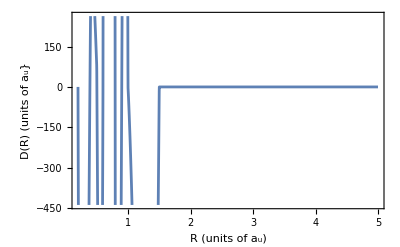

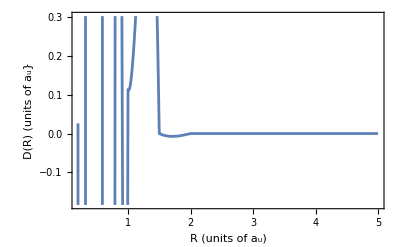

```mathematica
(*Plot[{dRPlus[r],dRMinus[r]},{r,.2,5}, PlotLabels->{"2p+ -> 1s+","2p+ -> 1s+"}, Frame->True,FrameLabel->{"R (units of a_u)", "D(R) (units of a_u}"} ]*)
dRPlus[.4]
Plot[{dRPlus[r]},{r,.2,5},  Frame->True,FrameLabel->{"R (units of a_u)", "D(R) (units of a_u}"} ]
Plot[{dRMinus[r]},{r,.2,5},  Frame->True,FrameLabel->{"R (units of a_u)", "D(R) (units of a_u}"} ]
```

```mathematica
(* Transition Amplitude *)
aR[x_,state1_, state2_, limit_]:=Module[{inputData, deltaV,dR, dV},
{inputData, dV}=GetInputData[state1,state2];
dR =CalcDR[inputData, limit];
deltaV[r_]:=dV[r];
4/3(dR[x])^2(deltaV[x])^3/c^3 
];
```

```mathematica
(* Energy  Range, for temperatures from 0K - 2K 
Subscript[k, B] T = 1/2 m v^2 = E, t in Kelvin  *)

energies = Interpolation[ Table[Subscript[k, B] atUofT T, {T,0,20,.5}],InterpolationOrder->3];
Subscript[k, aR][T_]:=Sqrt[2 Subscript[m, μ] (Subscript[k, B] atUofT  T- Subscript[v, s1][10])];
Plot[Subscript[k, aR][T],{T,0,2}, PlotLabels->Automatic]
```

-Graphics-

{-1.78973,InterpolatingFunction[…]}

InterpolatingFunction[…]

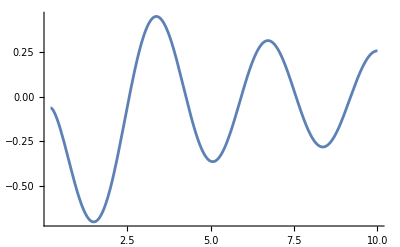

```mathematica
solF[m_]:=Sort[Transpose[NDEigensystem[1/r D[r D[ff[r],r],r] -(Subscript[v, s1][r]+m^2/r^2)ff[r],ff,{r,0.2, maxR}, 5,
Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.001}}}}]]][[1]];
solFAll[m_]:=Sort[Transpose[NDEigensystem[1/r D[r D[ff[r],r],r] -(Subscript[v, s1][r]+m^2/r^2)ff[r],ff,{r,0.2, maxR}, 5,
Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.001}}}}]]];
solF[0]
fff=solF[2][[2]]
Plot[fff[r],{r,0.2,10}]
```

```mathematica
(* 2D Schrodinger equation, m is a paramete #  (called J in 3D),
grab the lowest eigenvalue, i.e. value of k *)
solS1m=Sort[Transpose[NDEigensystem[1/r D[r D[ff[r],r],r] -(Subscript[v, s1][r]+#^2/r^2)ff[r],ff,{r,0.2, maxR}, 5,
Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.001}}}}]]][[1]]&;

solS1mAll=Sort[Transpose[NDEigensystem[1/r D[r D[ff[r],r],r] -(Subscript[v, s1][r]+#^2/r^2)ff[r],ff,{r,0.2, maxR}, 5,
Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.001}}}}]]]&;
(*solS2J[j_]:=Sort[Transpose[NDEigensystem[1/r D[r D[ff[r],r],r] -(Subscript[v, s2][r]+j^2/r^2)ff[r],ff[r],{r,0.2, limit}, 5,
Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.001}}}}]]];*)
(* Here m = 0 for 1S state *)


allS1ms = Sort[Map[solS1m, Table[i,{i,0,2,1}]]];
allS1ms
(*allS1msAll = Map[solS1mAll, Table[i,{i,0,2,1}]];
Length[allS1msAll]
allS1msAll *)
```

{{-1.78973,InterpolatingFunction[…]},{-1.73627,InterpolatingFunction[…]},{-1.10061,InterpolatingFunction[…]}}

```mathematica
allS1ks =  allS1ms[[All,1]];
allS1mFunc = allS1ms[[All,2]] ;
allS1mFunc
Plot[allS1mFunc[[2]][r],{r,.2,10}]
Subscript[k, A]=allS1ks;  
Subscript[k, A]
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

-Graphics-

{-1.78973,-1.73627,-1.10061}

```mathematica
fS1[m_,x_]:=allS1mFunc[[m]][x];
Plot[{fS1[0,r]},{r,.2,maxR}]
Plot[{fS1[1,r]},{r,.2,maxR}]
Plot[{fS1[2,r]},{r,.2,maxR}]
```

```mathematica
(* Compute the phase shift *)
(* 2D symptotic boundary conditions for large R *)
sApprox[k_, R_, m_]:=Sqrt[2/(Pi k R)]Cos[k R - Pi(m+1/2)/2+δ];
sApproxT[k_,m_] := Table[sApprox[k,R,m],{R,0, Limit}]
delta[k_,m_]:=ArcCos[Correlation[sApproxT[k,m],fS1T[m]]];

(* Calculate the integral *)
Subscript[η, s1pp][j_] := NIntegrate[(Abs[ fS1[j,x]])^2 aR[x,"s1", "p+", limit],{x,.2,limit}];
ScientificForm[Subscript[η, s1pp][1]]
```

```mathematica
Subscript[η, s1pm][j_] := NIntegrate[(Abs[ allS1JFunc[[j]][x] ])^2 aR[x,"s1", "p-", limit],{x,.2,limit}];
```

```mathematica
Subscript[η, s2pp][j_] := NIntegrate[(Abs[allS2JFunc[[j]][x]])^2 aR[x,"s2", "p+", limit],{x,.2,limit}];
```

```mathematica
Subscript[η, s2pm][j_] := NIntegrate[(Abs[allS2JFunc[[j]][x]])^2 aR[x,"s2", "p-", limit],{x,.2,limit}];
```

```mathematica
(* Cross Section *)

σ[r_]:=Pi/(Subscript[k, ar][r])^2 Sum[1-Exp[-4 Subscript[η, s1pp][j]],{j,0,1}];
Subscript[k, A]
Subscript[k, ar][1]
Plot[{Subscript[k, ar][r],σ[r]},{r,0.1,2}]
allS1Ks
```